## Tutorial 1: Getting Started.

## Welcome to Mathematica!

A taste of Mathematica’s capabilities

Introduction to Notebooks

Practicing getting help

Exploring the documentation center

Click on the forward arrow above to move to the next slide.

This tutorial is based on and uses materials from Wolfram Mathematica 7's “Learn with guided examples”.

## Using Mathematica as a calculator

You can use Mathematica as a calculator.

Move your cursor below this text until it becomes a horizontal cursor.  
Then click your mouse button.  
As soon as you start typing this will become a new input cell.

Now, type in 2+2.

Then press Shift+Enter  (Hold down Shift and press Enter).

You should see the answer appear.

Now try it again with something more complicated like 500! or 78^3.  
Remember: To calculate an expression, you must use Shift+Enter.

## Editing cells

Here is how you can use Mathematica to create a plot of the trigonometric function y=sin(x)+cos(3x).  
Press Shift+Enter to evaluate and see the plot.

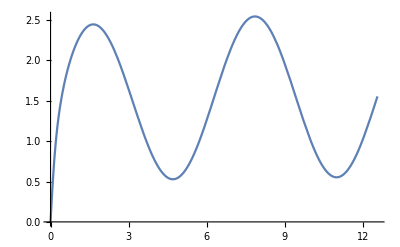

```mathematica
Plot[Sin[x]+ArcTan[5 x],{x,0,4Pi}]
```

When you have existing input cells, it’s easy to edit them, just as you would in a word processor.

Try changing Cos[3 x] to Cos[5 x] in the Plot command above and press Shift+Enter to re-evaluate the input.  The new output will replace the old.

Now try making some other changes to the input and see what happens.

A key to your success in this class will be exploring, experimenting, and not giving up when things don’t work right the first time.

## Keys to success: Capital Letters and [Square Brackets]

Now that you’ve learned how to get around in Mathematica, let’s look at the Mathematica language in more detail.
The most basic rule to know is that all built-in Mathematica functions start with CAPITAL LETTERS and enclose their arguments in [square, brackets].
Click in each of the following input cells and press Shift+Enter to see the result.

```mathematica
Plot[BesselJ[1,x],{x,0,30}]
```

Multiword function names use InternalCapitalization.

```mathematica
ListPlot[Table[Prime[n],{n,1,30}]]
```

Even standard math functions like sin and cos start with a capital letter.

```mathematica
Cos[0]
```

The constants e, i, and π also use capital letters.

```mathematica
N[{E,I,Pi}]
```

Because of this strict rule, you are free to use any name that starts with a lowercase letter for your own purposes. For example, you can use lowercase i as an index variable, as mathematicians like to do.

```mathematica
Table[i,{i,1,10}]
```

## Lists and {Curly Braces}

{Curly braces} are used to hold lists of expressions separated by commas. Anything can be part of a list. 
When you evaluate a list, each of the elements in the list is evaluated and the results are returned in another list.
Evaluate the examples below and you’ll see how this works.

```mathematica
{1,2,3,x,y,z}
```

```mathematica
{Integrate[x^2,x],Integrate[Sin[x],x],Integrate[Tan[x],x]}
```

Lists really can hold anything, including 2D or 3D graphics.

```mathematica
{Plot[Sin[x],{x,0,2Pi}],Plot[Sin[2x],{x,0,2Pi}],Plot[Sin[3x],{x,0,2Pi}],Plot[Sin[4x],{x,0,2Pi}]}
```

Evaluate this example to see three interesting knots in a list.

```mathematica
{KnotData["Trefoil"],KnotData["FigureEight"],KnotData["Stevedore"]}
```

Many types of output in Mathematica are interactive.
Click and drag the individual knots to see them from any angle!

Many functions allow you to create, operate on, or restructure lists. Here are just a few.

```mathematica
Sort[{3,1,2,5,4}]
```

```mathematica
Reverse[{1,2,3,4,5}]
```

```mathematica
Permutations[{1,2,3}]
```

Lists are the basic building blocks of Mathematica, so the upcoming tutorials will focus on how to create and work with them.

## Range Specifications

One important use of lists is to hold range specifications (also commonly known as iterators). Each of the commands below contains a set of three elements enclosed in curly brackets of the form {variable, min, max} or {variable, min, max, stepSize}.  
Evaluate each of the inputs on this page. Some of them are quite fun!

```mathematica
Table[i,{i,1,10}]
```

```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

```mathematica
Manipulate[Plot[Sin[n x],{x,0,2Pi}],{n,1,10}]
```

In Manipulate a step size can be specified. If it is omitted, the variable is allowed to take on a continuous range of values.

This example allows n to take on a continuous range of real numbers.

```mathematica
Manipulate[Expand[(1+x)^n], {n,0,100}]
```

Here the variable n is restricted to exact integers, allowing the Expand function to do its job.

```mathematica
Manipulate[Expand[(1 + x)^n], {n, 0, 100, 1}]
```

Manipulate has a very wide variety of interactive capabilities, extending well beyond the simple min - max range.

See the full documentation on Manipulate (which will open in a separate window).

## Fascinating Mathematica Examples

Here are some examples that show that Mathematica is much more than a programming language for mathematics. 
Some of these calculations take a while because they are accessing online information.

### Amazing mathematics visualizations

Plotting and interacting with three dimensional functions:

```mathematica
Manipulate[Plot3D[Sin[n x y],{x,0,3},{y,0,3}],{n,1,4}]
```

The whole Mandelbrot set: (from ref/MandelbrotSetPlot)

```mathematica
MandelbrotSetPlot[]
```

A transcendental periodic implicit surface: (from ref/ContourPlot3D)

```mathematica
ContourPlot3D[ Cos[x]Sin[y]+Cos[y]Sin[z]+Cos[z]Sin[x]==0,{x,-2π,2π}, {y,-2π,2π},{z,-2π,2π},ContourStyle->Directive[FaceForm[Orange,Red],Specularity[White,30]],Mesh->None]
```

Create an interactive Voronoi diagram with movable points. (from ref/VoronoiMesh)

```mathematica
DynamicModule[{p=RandomReal[{-1,1},{12,2}]},LocatorPane[Dynamic@p,Dynamic@VoronoiMesh[p,{{-1.5,1.5},{-1.5,1.5}},ImageSize->500],LocatorAutoCreate->True]]
```

### Sociological Analysis

A log-log scatter plot of GDP against population for all countries, with tooltips for country name : (from ref/CountryData)

```mathematica
ListLogLogPlot[Tooltip[{CountryData[#,"Population"],CountryData[#,"GDP"]},CountryData[#,"Name"]]&/@CountryData["Countries"]]
```

### Geographical Map and Data Integration

Show national flags of some countries and speak their names when clicked: (from ref/GeoGraphics)

```mathematica
GeoGraphics[{GeoStyling[{"Image",CountryData[#,"Flag"]}],EventHandler[Polygon[Entity["Country",#]],{"MouseClicked":>Speak[#]}]}&/@{"France","Germany","Italy","Spain"}]
```

### Image Processing

Adjust Colors in an image (from ref/ImageAdjust)

```mathematica
i=-Graphics-;
```

```mathematica
Table[ImageAdjust[i,c],{c,{-2,-1/2,1/2,2}}]
```

### Financial Analysis

Plot the stock price for GE since January 1, 2000:  (From ref/FinancialData)

```mathematica
DateListPlot[FinancialData["GE","Jan. 1, 2000"]]
```

### Social Network Analysis

Show communities in a social network graph: (from ref/CommunityGraphPlot)

```mathematica
CommunityGraphPlot[ExampleData[{"NetworkGraph","DolphinSocialNetwork"}]]
```

### Text Analysis

Summarize a piece of text: (from ref/WordCloud)

```mathematica
text=ExampleData[{"Text","USConstitution"}];
WordCloud[text]
```

### Machine Learning

Use a clustering analysis to analyze handwriting (from ref/Classify)

Train a digit recognizer on 100 examples from the MNIST database of handwritten digits:

```mathematica
digit=Classify[
{-Graphics-->2,-Graphics-->5,-Graphics-->8,-Graphics-->0,-Graphics-->2,-Graphics-->7,-Graphics-->5,-Graphics-->1,-Graphics-->3,-Graphics-->0,-Graphics-->3,-Graphics-->9,-Graphics-->6,-Graphics-->2,-Graphics-->8,-Graphics-->2,-Graphics-->0,-Graphics-->6,-Graphics-->6,-Graphics-->1,-Graphics-->1,-Graphics-->7,-Graphics-->8,-Graphics-->5,-Graphics-->0,-Graphics-->4,-Graphics-->7,-Graphics-->6,-Graphics-->0,-Graphics-->2,-Graphics-->5,-Graphics-->3,-Graphics-->1,-Graphics-->5,-Graphics-->6,-Graphics-->7,-Graphics-->5,-Graphics-->4,-Graphics-->1,-Graphics-->9,-Graphics-->3,-Graphics-->6,-Graphics-->8,-Graphics-->0,-Graphics-->9,-Graphics-->3,-Graphics-->0,-Graphics-->3,-Graphics-->7,-Graphics-->4,-Graphics-->4,-Graphics-->3,-Graphics-->8,-Graphics-->0,-Graphics-->4,-Graphics-->1,-Graphics-->3,-Graphics-->7,-Graphics-->6,-Graphics-->4,-Graphics-->7,-Graphics-->2,-Graphics-->7,-Graphics-->2,-Graphics-->5,-Graphics-->2,-Graphics-->0,-Graphics-->9,-Graphics-->8,-Graphics-->9,-Graphics-->8,-Graphics-->1,-Graphics-->6,-Graphics-->4,-Graphics-->8,-Graphics-->5,-Graphics-->8,-Graphics-->0,-Graphics-->6,-Graphics-->7,-Graphics-->4,-Graphics-->5,-Graphics-->8,-Graphics-->4,-Graphics-->3,-Graphics-->1,-Graphics-->5,-Graphics-->1,-Graphics-->9,-Graphics-->9,-Graphics-->9,-Graphics-->2,-Graphics-->4,-Graphics-->7,-Graphics-->3,-Graphics-->1,-Graphics-->9,-Graphics-->2,-Graphics-->9,-Graphics-->6}]
```

ClassifierFunction[…]

Use the classifier to recognize unseen digits:

```mathematica
digit[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]
```

Analyze probabilities of a misclassified example:

```mathematica
digit[-Graphics-, "TopProbabilities"]
```

### Identify an image

Identify what type of dog is present in the image: (from ref/ImageIdentify)

```mathematica
ImageIdentify[-Graphics-,Entity["Species","Infraspecies:CanisLupusFamiliaris"]]
```

### Music Generation and Sound Analysis

A simple function that gives a "sound effect".  Evaluate the code and then click on the “Play” button in the box that appears. (Make sure your speakers are on.) (from ref/Play)

```mathematica
Play[Sum[Sin[1000 Sqrt[n] t(1+Cos[n t])],{n,10}],{t,0,2}]
```

Evaluate this text to voice cell. (see ref/Speak)

```mathematica
Speak["Isn't Mathematica amazing?"]
```

## Getting Help

The Documentation Center is the starting point for all help, including tutorials, guide pages, and function home pages. It is a resource that sets Mathematica apart from other programming languages and is always available from the top of the Help menu.

If you already know or can guess the function you need, and just want to be reminded of its arguments, the ? operator is a quick way to get information without opening a new window.

```mathematica
?Integrate
```

In Desktop Mathematica, you can hover over any function name to pull up this information or access its function reference page.

## Helpful clues from Mathematica

Mathematica automatically colors symbols, brackets, and operators to indicate errors or likely errors. When you type a function name, it starts out blue and turns black when it matches the name of a built-in or user-defined symbol.

```mathematica
P
Pl
Plo
Plot
Plot3
Plot3D
```

A blue symbol is not necessarily an error; it simply means that the symbol does not currently have any value or definition associated with it. For example, before the following line is evaluated, the symbol name on the left-hand side is blue, but after evaluation it turns black because a value has been assigned to it. Try this now by evaluating the input cell.

```mathematica
value=7;
```

Unmatched brackets or parentheses are given a reddish purple color that indicates a syntax error.

```mathematica
Table[i,{i,1,10]
```

If you nevertheless evaluate such an input, emphasis is added to the unmatched elements in the form of a yellow background.Clicking the yellow symbol near the cell bracket will print out an error message describing the problem (but only after you have evaluated the input).

```mathematica
Table[i,{i,1,10]
```

When a function requires more arguments than you' ve given it, a red caret indicates where more are needed. Conversely, when a function has been given too many arguments, the excess arguments are colored red.

```mathematica
Integrate[x]
Sin[a,b]
```

Incorrect option names are colored red.

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotArea->{-1,1}]
```

Local variables of several types are specially colored : in each case below, the variable x is colored (or italicized) because during evaluation it will be given a local value that overrides any global value that may be assigned to it.

```mathematica
func[x_]:=x^2
Module[{x},x+2]
Table[x,{x,0,10}]
```

## Upward and Onward

Where to go from here?  Explore!  I suggest the following

Explore the Documentation Center.  (Click on Help > Documentation Center)
This is the best place to:

Learn how to use a function in Mathematica.

Get ready-to-go examples to practice with and build on.

Explore Mathematica's capabilities.

Especially explore the documentation on: Manipulate and Plot.

Go from command to command using the “See Also” links at the bottom of an entry.

Visit the Demonstrations Project online.   (http://www.demonstrations.wolfram.com/)

See examples of Mathematica in action in many fields of science and mathematics.

Visit Wolfram Alpha to get started, and then download as "Live Mathematica" (bottom of output) to modify and edit in Mathematica.